We want to solve the integral
2(1-Cos(2 pi y_1))/|y|^{2H+d} over all of R^d
which can be done in spherical coordinates

```mathematica
(* 1 d *)
```

```mathematica
2Integrate[(1-Cos[2π k])/((k^2)^(H+1/2)),{k,-∞,∞},Assumptions->0<H<1]
```

-2^(2+2 H) π^(2 H) Cos[H π] Gamma[-2 H]

```mathematica
FullSimplify[Cos[π H]/Sin[2π H]]
```

1/2 Csc[H π]

```mathematica
(* 2d *)
```

```mathematica
Integrate[(1-Cos[2π r Cos[θ]]),{θ,0,2π},Assumptions->r>0]
```

2 (π-π BesselJ[0,2 π r])

```mathematica
2 Integrate[2 (π-π BesselJ[0,2 π r])r/r^(2H+2),{r,0,∞}]
```

ConditionalExpression[-(2 π^(1+2 H) Gamma[-H])/Gamma[1+H], 0<Re[H]<1]

```mathematica
-(2 π^(1+2 H) Gamma[-H])/Gamma[1+H]//TeXForm
```

```mathematica
FullSimplify[Gamma[-H]/Gamma[1+H]]
```

Gamma[-H]/Gamma[1+H]

```mathematica
(* 3 d *)
```

```mathematica
Integrate[Sin[ϕ1](1-Cos[2π r Cos[ϕ1]]),{ϕ1,0,π},Assumptions->{r>0}]
```

2-Sin[2 π r]/(π r)

```mathematica
2 Integrate[(2-Sin[2 π r]/(π r))r^2/r^(2H+3),{r,0,∞},Assumptions->0<H<1]
```

2^(2+2 H) π^(2 H) Cos[H π] Gamma[-1-2 H]

```mathematica
FullSimplify[Cos[π H]/Sin[π+π 2 H]]
```

-1/2 Csc[H π]

```mathematica
(* n-d *)
```

```mathematica
Integrate[Sin[ϕ1]^(d-2)(1-Cos[2π r Cos[ϕ1]]),{ϕ1,0,π},Assumptions->{r>0,d>2}]
```

-1/Gamma[d/2]√π Gamma[1/2 (-1+d)] (-1+Hypergeometric0F1[d/2,-π^2 r^2])

```mathematica
2Integrate[(-1/Gamma[d/2] √π Gamma[1/2 (-1+d)] (-1+Hypergeometric0F1[d/2,-π^2 r^2]))r^(-1-2H),{r,0,∞},Assumptions->{d>2,H<1}]
```

ConditionalExpression[-(π^(1/2+2 H) Gamma[1/2 (-1+d)] Gamma[-H])/Gamma[d/2+H], H>0]

```mathematica
Integrate[Sin[ϕ]^n,{ϕ,0,π}]
```

ConditionalExpression[(√π Gamma[(1+n)/2])/Gamma[1+n/2], Re[n]>-1]

```mathematica
(* 3d from high dim integrals *)
fh[H_]=-2π(π^(1/2+2 H) Gamma[1/2 (-1+d)] Gamma[-H])/Gamma[d/2+H]/.d->3
```

```mathematica
2π(-(2 π^(3/2+2 H) Gamma[-H])/Gamma[3/2+H]
```

```mathematica
(* 3d from spherical coordinates *)
```

```mathematica
fs[H_]:=2π 2^(2+2 H) π^(2 H) Cos[H π] Gamma[-1-2 H]
```

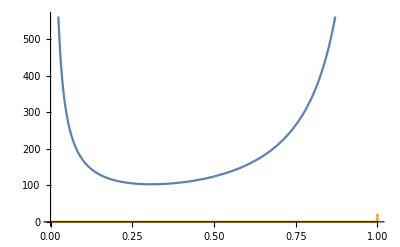

```mathematica
Plot[{fs[H],fs[H]-fh[H]},{H,0,1}]
```

```mathematica
a=.5*Sqrt[12]
```

1.73205

```mathematica
(* nd *)
```

```mathematica
(* variance, 1d *)
```

```mathematica
Integrate[(k^2+ε^2)^(-H-1/2),{k,-∞,∞},Assumptions->{ε>0,0<H<1}]
```

(√π ε^(-2 H) Gamma[H])/Gamma[1/2+H]

```mathematica
(* variance, 2d *)
```

```mathematica
Integrate[k(k^2+ε^2)^(-H-2/2),{k,0,∞},Assumptions->{ε>0,0<H<1}]
```

ε^(-2 H)/(2 H)

```mathematica
(* times 2π *)
```

```mathematica
(* variance, general d *)
```

```mathematica
Integrate[k^(d-1)(k^2+ε^2)^(-H-d/2),{k,0,∞},Assumptions->{ε>0,0<H<1,d>2}]
```

(ε^(-2 H) Gamma[d/2] Gamma[H])/(2 Gamma[d/2+H])

```mathematica
(* times the n-surface S_{n-1} *)
```

```mathematica
(2 π^(d/2))/Gamma[d/2](ε^(-2 H) Gamma[d/2] Gamma[H])/(2 Gamma[d/2+H])
```

(π^(d/2) ε^(-2 H) Gamma[H])/Gamma[d/2+H]